```mathematica
ClearAll["Global`*"];
```

```mathematica
(*initialization*)

(* for rational iteration *)
(* returns x^th number in the Calkin-Wilf sequence, see https://en.wikipedia.org/wiki/Calkin%E2%80%93Wilf_tree#Breadth_first_traversal *)
q[x_]:=Module[{b},
b=ToString[BaseForm[x,2]];
FromContinuedFraction[RunLengthEncode[Reverse[StringPart[b,1;;StringPosition[b," "][[1,1]]-2;;1]]]]
]
RunLengthEncode[x_List]:=If[First[x]=="1",Length[#]&/@Split[x],Join[{0},Length[#]&/@Split[x]]]

(* given rational (r,x), returns (m,y) that is a solution to S *)
ϕ[r_,x_]:={(-4-4 r-r^2-4 x^2-2 r x^2+x^4)/(8 r),(-4+r^2-4 x^2+x^4)/(2 r)};
```

We start with
	S: y^2==2 x^4+8m x^2+16 m^2+16m.
Or equivalently,
	S: y^2==(x^2+4m+2)^2+x^4-4 x^2-4.

Then we apply the transformation
	τ: y↦Y/Z, 4m+x^2+2↦M/Z
with inverse
	τ^-1: Y/Z↦y, (M-2Z-x^2 Z)/(4Z)↦m.
This gives us the conic
	C: Y^2==M^2+(x^4-4 x^2-4)Z^2.
After this, we use the birational map
	σ : (r,x)↦(Y:M:Z)=(x^4+r^2-4 x^2-4:x^4-r^2-4 x^2-4:2r).
	
So we have a solution to the conic for every rational (r,x), by taking τ^-1(σ(r,x)). For easier notation, let ϕ=τ^-1∘σ. Then
	ϕ: (r,x) ↦(m,y)=((-4-4 r-r^2-4 x^2-2 r x^2+x^4)/(8 r),(-4+r^2-4 x^2+x^4)/(2 r)).

```mathematica
(* Indeed, σ works *)
Y=x^4+r^2-4 x^2-4;
M=x^4-r^2-4 x^2-4;
Z=2r;
{Y^2,M^2+(x^4-4 x^2-4)Z^2}//Expand
```

{16-8 r^2+r^4+32 x^2-8 r^2 x^2+8 x^4+2 r^2 x^4-8 x^6+x^8,16-8 r^2+r^4+32 x^2-8 r^2 x^2+8 x^4+2 r^2 x^4-8 x^6+x^8}

```mathematica
(* finding τ^-1 *)
Solve[{
y==Y/Z,
x^2+4m+2==M/Z
},{m,y}]
```

{{m→(M-2 Z-x^2 Z)/(4 Z),y→Y/Z}}

```mathematica
(* finding ϕ = τ^-1∘σ *)
Y=x^4+r^2-4 x^2-4;
M=x^4-r^2-4 x^2-4;
Z=2r;
(*  (m,y) =   *){(M-2 Z-x^2 Z)/(4 Z),Y/Z}
```

{(-4-4 r-r^2-4 x^2-2 r x^2+x^4)/(8 r),(-4+r^2-4 x^2+x^4)/(2 r)}

```mathematica
f3NR={}; (* record parameter values that give f^3,f^2 newly reducible *)
f2NR={};
f1R={};
Do[Do[

m=ϕ[r,d][[1]];
γ=Sqrt[2 d^4+8m d^2+16 m^2+16m](-3/16 d^6-m/2 d^4-m^2/2 d^2-m/2 d^2)+17/64 d^8+(5m)/4 d^6+(11 m^2)/4 d^4+(7m)/4 d^4+2 m^3 d^2+2 m^2 d^2-m;
f[x_]:=(x-γ)^2+γ+m;
If[IrreduciblePolynomialQ[f[x]],
If[IrreduciblePolynomialQ[f[f[x]]],
AppendTo[f3NR,{r,d}];
,
AppendTo[f2NR,{r,d}];
]
,
AppendTo[f1R,{r,d}];
]

,{r,0,100,1/16}],{d,1/2,1/2,1}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1/8+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression -3/1024+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::ivar: Indeterminate is not a valid variable.

IrreduciblePolynomialQ::poly: Indeterminate is not a polynomial.

```mathematica
f1R//MatrixForm
```

(21/8 | 1/2
17/4 | 1/2
49/8 | 1/2
33/4 | 1/2
85/8 | 1/2
53/4 | 1/2
129/8 | 1/2
77/4 | 1/2
181/8 | 1/2
105/4 | 1/2
241/8 | 1/2
137/4 | 1/2
309/8 | 1/2
173/4 | 1/2
385/8 | 1/2
213/4 | 1/2
469/8 | 1/2
257/4 | 1/2
561/8 | 1/2
305/4 | 1/2
661/8 | 1/2
357/4 | 1/2
769/8 | 1/2)

```mathematica
(* plotting gamma over (m,x) (m on horizontal axis) *)
T=Table[{},{i,-100,100}];
Do[Do[
m=ϕ[r,d][[1]];
γ=Sqrt[2 d^4+8m d^2+16 m^2+16m](-3/16 d^6-m/2 d^4-m^2/2 d^2-m/2 d^2)+17/64 d^8+(5m)/4 d^6+(11 m^2)/4 d^4+(7m)/4 d^4+2 m^3 d^2+2 m^2 d^2-m;
AppendTo[T[[-d+101]],N[γ]];
,{r,-100,100}],{d,100,-100,-1}];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 200000000+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression -187500000000+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 192119202+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

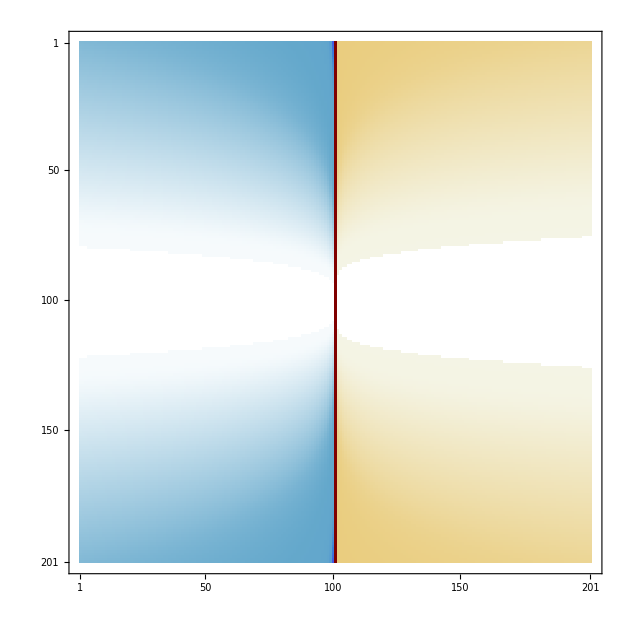

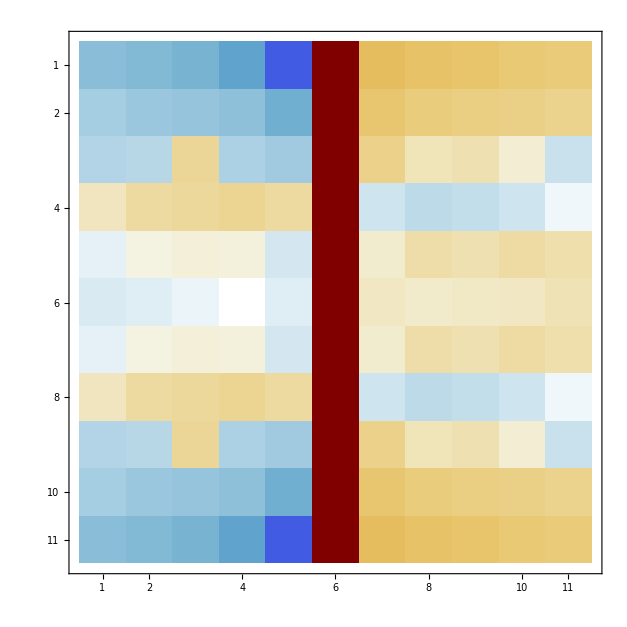

```mathematica
MatrixPlot[T]
MatrixPlot[Transpose[Transpose[T[[96;;106]]][[96;;106]]]]
```

```mathematica
(*  If r = 2 q^2+2q+2((d-1)/2)^2+2((d-1)/2)-1 for some q∈ℚ, Then f is reducible!  *)
m=ϕ[2 q^2+2q+2((d-1)/2)^2+2(d-1)/2-1,d][[1]];
γ=Sqrt[2 d^4+8m d^2+16 m^2+16m](-3/16 d^6-m/2 d^4-m^2/2 d^2-m/2 d^2)+17/64 d^8+(5m)/4 d^6+(11 m^2)/4 d^4+(7m)/4 d^4+2 m^3 d^2+2 m^2 d^2-m//Simplify
```

1/256 (68 d^8+(16 (d^4+(1+2 q)^4+6 (d+2 d q)^2))/(-3+d^2+4 q+4 q^2)-(28 d^4 (d^4+(1+2 q)^4+6 (d+2 d q)^2))/(-3+d^2+4 q+4 q^2)-(20 d^6 (d^4+(1+2 q)^4+6 (d+2 d q)^2))/(-3+d^2+4 q+4 q^2)+(2 d^2 (d^4+(1+2 q)^4+6 (d+2 d q)^2)^2)/((-3+d^2+4 q+4 q^2)^2)+(11 d^4 (d^4+(1+2 q)^4+6 (d+2 d q)^2)^2)/(4 (-3+d^2+4 q+4 q^2)^2)-(d^2 (d^4+(1+2 q)^4+6 (d+2 d q)^2)^3)/(8 (-3+d^2+4 q+4 q^2)^3)-1/(8 (-3+d^2+4 q+4 q^2)^2)d^2 √(((5 d^4+(1+2 q)^2 (-7+4 q+4 q^2)+d^2 (-22+8 q+8 q^2))^2)/((-3+d^2+4 q+4 q^2)^2)) (81 d^8+(1+2 q)^4 (-7+4 q+4 q^2)^2+4 d^6 (-157+92 q+92 q^2)-4 (d+2 d q)^2 (-83+56 q+72 q^2+32 q^3+16 q^4)+2 d^4 (563-904 q-728 q^2+352 q^3+176 q^4)))

```mathematica
(* The thing under the square root (say, a) has sign unchanged after √(a^2), because: *)
Reduce[(5 d^4+(1+2 q)^2 (-7+4 q+4 q^2)+d^2 (-22+8 q+8 q^2))/(-3+d^2+4 q+4 q^2)≥0,{d,q},Reals]
```

True

```mathematica
(* so, *)
(γ=1/256 (68 d^8+(16 (d^4+(1+2 q)^4+6 (d+2 d q)^2))/(-3+d^2+4 q+4 q^2)-(28 d^4 (d^4+(1+2 q)^4+6 (d+2 d q)^2))/(-3+d^2+4 q+4 q^2)-(20 d^6 (d^4+(1+2 q)^4+6 (d+2 d q)^2))/(-3+d^2+4 q+4 q^2)+(2 d^2 (d^4+(1+2 q)^4+6 (d+2 d q)^2)^2)/((-3+d^2+4 q+4 q^2)^2)+(11 d^4 (d^4+(1+2 q)^4+6 (d+2 d q)^2)^2)/(4 (-3+d^2+4 q+4 q^2)^2)-(d^2 (d^4+(1+2 q)^4+6 (d+2 d q)^2)^3)/(8 (-3+d^2+4 q+4 q^2)^3)-1/(8 (-3+d^2+4 q+4 q^2)^2)d^2 (5 d^4+(1+2 q)^2 (-7+4 q+4 q^2)+d^2 (-22+8 q+8 q^2))/(-3+d^2+4 q+4 q^2) (81 d^8+(1+2 q)^4 (-7+4 q+4 q^2)^2+4 d^6 (-157+92 q+92 q^2)-4 (d+2 d q)^2 (-83+56 q+72 q^2+32 q^3+16 q^4)+2 d^4 (563-904 q-728 q^2+352 q^3+176 q^4))))//Simplify
```

-1/(1024 (-3+d^2+4 q+4 q^2)^2)(d^10 (1+2 q)^2-64 (1+2 q)^4 (-3+4 q+4 q^2)-4 d^8 (1+2 q)^2 (5+4 q+4 q^2)+2 d^6 (11+228 q+500 q^2+736 q^3+848 q^4+576 q^5+192 q^6)+(d+2 d q)^2 (1137-1456 q-1104 q^2-64 q^3-1696 q^4-1280 q^5+768 q^6+1024 q^7+256 q^8)-4 d^4 (13+160 q-448 q^2-1216 q^3-352 q^4+1024 q^5+1536 q^6+1024 q^7+256 q^8))

```mathematica
(* And then this is a rational square *)
-γ-m//Simplify
```

(d^2 (1+2 q)^2 (d^4+(1+2 q)^2 (-7+4 q+4 q^2)-2 d^2 (5+4 q+4 q^2))^2)/(1024 (-3+d^2+4 q+4 q^2)^2)